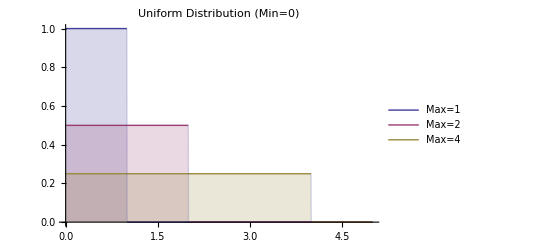
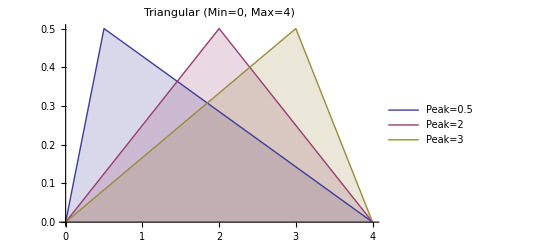
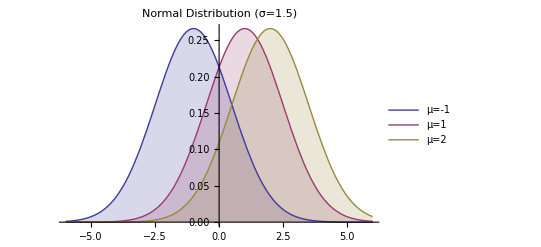
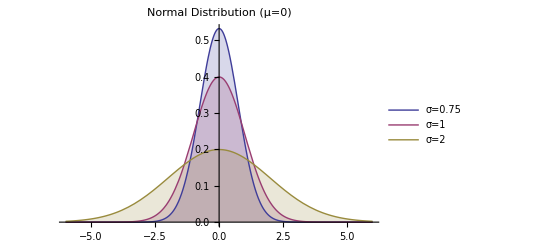
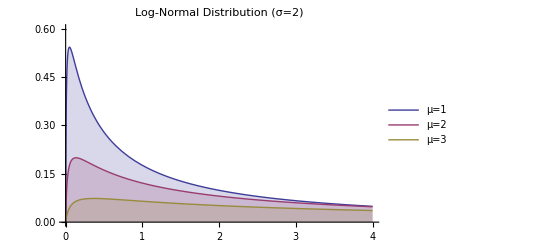
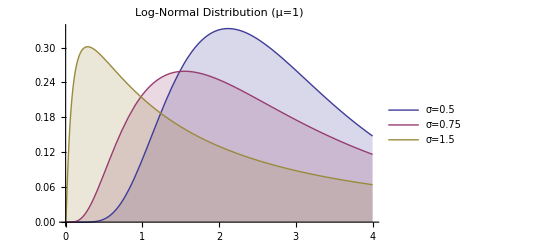
-Graphics- | -Graphics-
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
dists = TableForm[{{
v={1,2,4};
Plot[Evaluate@Table[PDF[UniformDistribution[{0,max}],x],{max,v}],{x,0,5},PlotRange->All,Filling->Axis,PlotLegends->Placed[
"Max="<>ToString[#]&/@ v,Below], PlotLabel->"Uniform Distribution (Min=0)"],

v={0.5,2,3};
Plot[Evaluate@Table[PDF[TriangularDistribution[{0,4},c],x],{c,v}],{x,0,4},Filling->Axis,Exclusions->None, PlotLegends->Placed[
"Peak="<>ToString[#]&/@ v,Below],PlotLabel->"Triangular (Min=0, Max=4)"]

},
{

v={-1,1,2};
Plot[Evaluate@Table[PDF[NormalDistribution[μ,1.5],x],{μ,v}],{x,-6,6},Filling->Axis,PlotLegends->Placed[
"μ="<>ToString[#]&/@ v,Below], PlotLabel->"Normal Distribution (σ=1.5)"],

v= {.75,1,2};
Plot[Evaluate@Table[PDF[NormalDistribution[0,σ],x],{σ,v}],{x,-6,6},Filling->Axis,PlotLegends->Placed[
"σ="<>ToString[#]&/@ v,Below], PlotLabel->"Normal Distribution (μ=0)"]

},
{

v={1,2,3};
Plot[Evaluate@Table[PDF[LogNormalDistribution[μ,2],x],{μ,v}],{x,0,4},Filling->Axis,PlotRange->{0,.6},PlotLegends->Placed[
"μ="<>ToString[#]&/@ v,Below], PlotLabel->"Log-Normal Distribution (σ=2)"],

v={0.5,0.75,1.5};
Plot[Evaluate@Table[PDF[LogNormalDistribution[1,σ],x],{σ,v}],{x,0,4},Filling->Axis,PlotLegends->Placed[
"σ="<>ToString[#]&/@ v,Below], PlotLabel->"Log-Normal Distribution (μ=1)"]

}
}]
Print[dists]
```

```mathematica
Export["Distributions.png", dists, ImageSize->1200]
```

Distributions.png

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["distributions.png"]]]
```